## This section provides only the functions we actually use in the final product. Later sections include also the prototypes and experiments

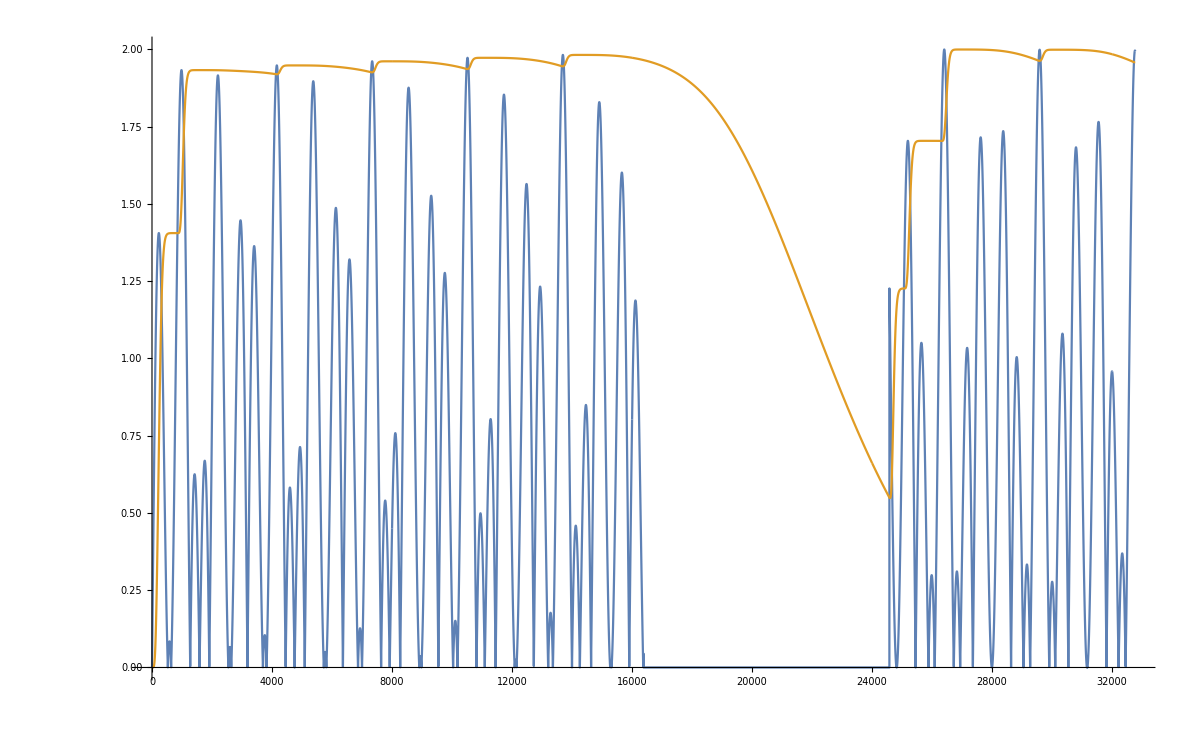

```mathematica
releaseOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


EnvelopeProcessSeparateTriple[X_, attackTime_, releaseTime_]:=Module[{fMultiplier,Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =1/attackTime;
releaseFc = 1/releaseTime;
Q=0.5;
fMultiplier = 1.5;

output =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate]; 


output
]

sampleRate = 48000;
length = 2^15;
input = Table[Sin[15 2π N[x]]+Sin[60.445 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[{Abs[input],EnvelopeProcessSeparateTriple[Abs[input],0.005,0.250]}]
```

## This section contains code we use for the demo video

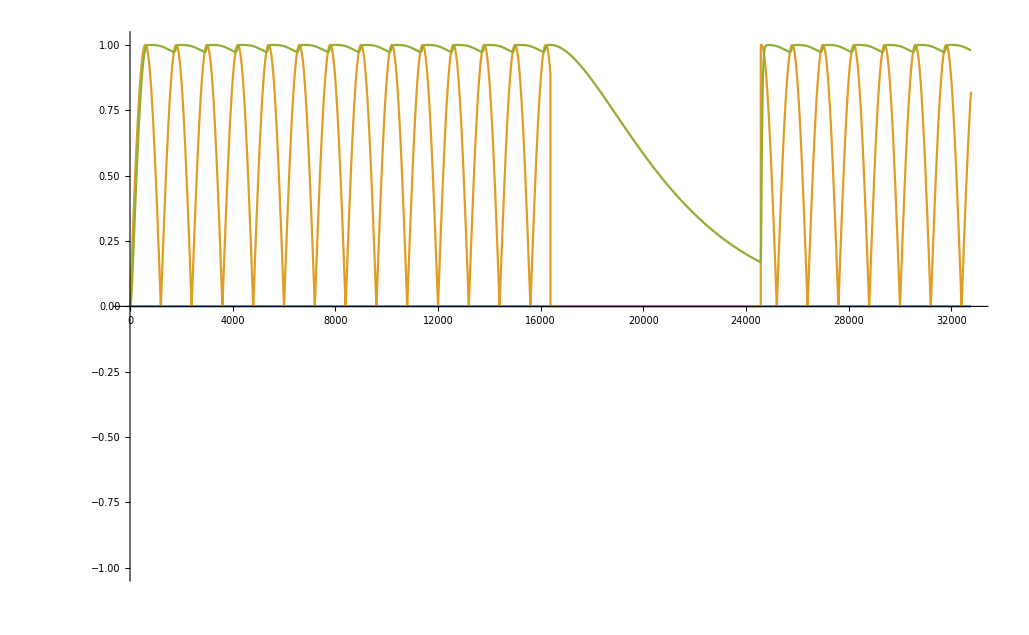

```mathematica
EnvelopeProcessSeparateSingle[X_, attackTime_, releaseTime_]:=Module[{fMultiplier,Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;

attackFc =1/attackTime;
releaseFc = 1/releaseTime;
Q=0.5;
fMultiplier = 1.5;

output =
attackOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate]; 

output
]

sampleRate = 48000;
length = 2^15;
input = Table[Sin[20 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0; 


 ListLinePlot[{0input,Abs[input],EnvelopeProcessSeparateSingle[Abs[input],0.005,0.500]},PlotRange->1.01*{-1,1}]
```

## The following sections show the experiments we used before settling on a final method.

```mathematica
sampleRate = 48000;

svf2Q=0.805538281842;
svf1Q =0.521934581669;
svf2FScale =1.60335751622;
svf1FScale=1.43017155999;

(*
svf2Q=0.5;
svf1Q =0.5;
svf2FScale =1.0;
svf1FScale=1.0;
*)

(* member variables for section 1 *)
ic1eq1 =0;
ic2eq1=0;
k1=1/svf1Q;
a11 = 0;
a21=0;
a31= 0;
gPrev1=0;

(* member variables for section 2 *)
ic1eq2 =0;
ic2eq2=0;
k2=1/svf2Q;
a12 = 0;
a22=0;
a32= 0;
gPrev2=0;

(* member variables for Chamberlain *)
z1=1;
z2=1;
F = 1;
Dd = 1/svf1Q;
Fnew = 1;
xz2Prev =1;


(* functions for setting filter coefficients *)
setSection1[ωc_]:=Module[{g},
g = Tan[π ωc / sampleRate];
a11 = 1/(1+g*(g+k1));
a21=g*a11;
a31= g*a21;
]


setSection1SmoothlyG[ωc_]:=Module[{g},

g = Tan[π ωc / sampleRate];
ic1eq1 = ic1eq1 (gPrev1 / g);
a11 = 1/(1+g*(g+k1));
a21=g*a11;
a31= g*a21;

gPrev1 = g;
]


setSection2SmoothlyG[ωc_]:=Module[{g},

g = Tan[π ωc / sampleRate];
ic1eq2 = ic1eq2 (gPrev2 / g);
a12 = 1/(1+g*(g+k1));
a22=g*a12;
a32= g*a22;

gPrev2 = g;
]


setSection1SmoothlyA[ωc_]:=Module[{g,a21Prev},
(* store the previous a21 before updating it *)
a21Prev = a21;

g = Tan[π ωc / sampleRate];

a11 = 1/(1+g*(g+k1));
a21=g*a11;
a31= g*a21;

ic1eq1 = ic1eq1 (a21Prev / a21);
]

setSection2[ωc_]:=Module[{g},
g = Tan[π ωc / sampleRate];
a12 = 1/(1+g*(g+k2));
a22=g*a12;
a32= g*a22;
]


(* main filter processing functions *)
simperSVF1[x_]:=Module[{v3,v1,v2},

(* process *)
v3=x- ic2eq1;
v1=a11*ic1eq1 + a21*v3;
v2 = ic2eq1 + a21*ic1eq1+ a31*v3;

(* update *)
ic1eq1 = 2*v1-ic1eq1;
ic2eq1=2*v2-ic2eq1;

v2
]


simperSVF2[x_]:=Module[{v3,v1,v2},

(* process *)
v3 =x- ic2eq2;
v1 =a12*ic1eq2 + a22*v3;
v2 = ic2eq2 + a22*ic1eq2+ a32*v3;

(* update *)
ic1eq2 = 2*v1-ic1eq2;
ic2eq2=2*v2-ic2eq2;

v2
]


releaseOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = 0;
attackMode = True;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: follow input exactly *)
attackMode = True;
output[[i]] = X[[i]],

(* release mode: set gradient to zero and start from last value *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False;ic1=0; ic2=prevY];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
];

prevY= output[[i]];
];

output
]


attackOnlySVF[X_,fc_,Q_,sr_]:=Module[{prevY,prevY2,i,ic1, ic2, a1, a2, a3, v1, v2, v3,g,gInv,k,attackMode,output},
output =X;
g = Tan[π fc /sr];
gInv = 1.0/g;
k=1/Q;
a1 = 1/(1+g*(g+k));
a2=g*a1;
a3= g*a2;
prevY = prevY2 =0;
attackMode = False;
ic1 = ic2 = v1 = v2 = v3 = 0;

For[i=1, i<=Length[X], i++,
If[X[[i]] > prevY, 

(* attack mode: filter *)
(* if this is the first sample of the attack, switch to attack mode *)
If[!attackMode,
attackMode = True; ic1 = 0.5*(prevY-prevY2)*gInv; ic2 = prevY;
];
(* process svf *)
v3 =X[[i]]- ic2;
v1 =a1*ic1 + a2*v3;
v2 = ic2 + a2*ic1+ a3*v3;
(* update state *)
ic1 = 2*v1-ic1;
ic2=2*v2-ic2;
(* output *)
output[[i]] = v2;
,

(* release mode: copy input to output *)
If[attackMode,
(* if this is the first sample of the release, switch to release mode and manually update the state variables *)
(* f(i) = x, f'(i) = 0 *)
attackMode = False];
output[[i]] = X[[i]];
];

prevY2 = prevY;
prevY= output[[i]];
];

output
]


setSmoothlyChamberlain[ωc_]:=Module[{},
Fnew = 2 Sin[π ωc / sampleRate];

(*
(* keep the gradient continuous when F changes *)
z1= z1 *F / Fnew;
(* z2 = z2 * F / Fnew; *)
F = Fnew;
*)
]


chamberlainSVF[x_]:=Module[{bi,ci,ai},

bi=z2 + F z1; (* low pass *)
ci = N[x] - bi - Dd z1; (* high pass *) 
ai = z1 + F ci; (* band pass *)

(* it's safe to take fc down when z1 changes sign *)
If[Fnew < F &&ai *z1 < 0,F = Fnew;z1 = z1 * F / Fnew];

(* update *)
z1 = ai;
z2 = bi;

(* it's safe to go up in frequency when (x-z2) changes sign ??? *)
If[Fnew > F  &&(x-z2) *xz2Prev < 0 ,F = Fnew ;z1 = z1 * F / Fnew];
 xz2Prev = (x-z2); 

(* it's always safe to go up in frequency *)
(*If[Fnew > F, F = Fnew(*,z1=z1 * F / Fnew*)];*)

(* output *)
bi
]


length = 2^12;
input = Table[Sin[20 2π x],{x,0,1,1/length}];

highFc = 1000;
lowFc = 100;
numSamplesHigh = 200;
freqChangeTestNoSmoothing[l_]:=Module[{output,g,i},
output = l;
For[i=1, i<=length, i++,
output[[i]] = simperSVF1[l[[i]]];
If[Mod[i,575]<numSamplesHigh,setSection1[highFc],setSection1[lowFc]];
];

output
]

freqChangeTestWithSmoothingG[l_]:=Module[{output,g,i},
setSection1SmoothlyG[highFc svf1FScale];
setSection2SmoothlyG[highFc svf1FScale];
output = l;
For[i=1, i<=length, i++,
output[[i]] = simperSVF1[l[[i]]];
output[[i]] = simperSVF2[output[[i]]];
If[Mod[i,575]<numSamplesHigh,
setSection1SmoothlyG[highFc svf1FScale];setSection2SmoothlyG[highFc svf1FScale],
setSection1SmoothlyG[lowFc svf1FScale];setSection2SmoothlyG[lowFc svf2FScale]];
];

output
]

freqChangeTestWithSmoothingA[l_]:=Module[{output,g,i},
output = l;
For[i=1, i<=length, i++,
output[[i]] = simperSVF1[l[[i]]];
If[Mod[i,575]<numSamplesHigh,setSection1SmoothlyA[highFc],setSection1SmoothlyA[lowFc]];
];

output
]

freqChangeTestWithSmoothingChamberlain[l_]:=Module[{output,g,i},
output = l;
For[i=1, i<=length, i++,
output[[i]] = chamberlainSVF[l[[i]]];
If[Mod[i,575]<numSamplesHigh,setSmoothlyChamberlain[highFc],setSmoothlyChamberlain[lowFc]];
];

output
]
```

## There are glitches when we change the frequency too abruptly

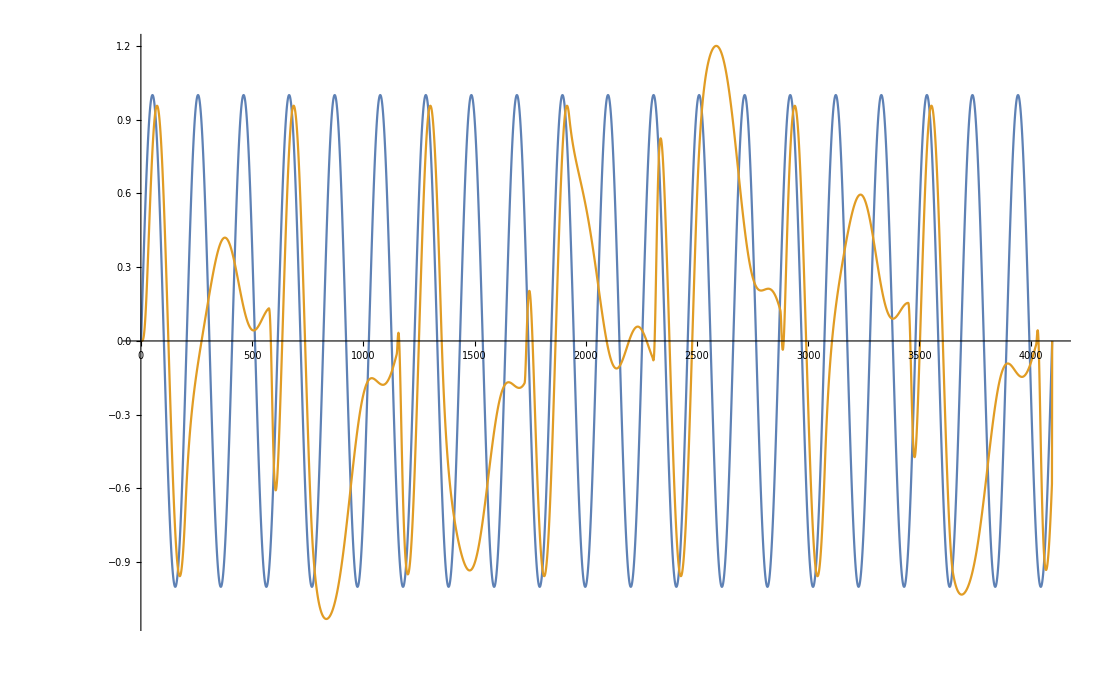

```mathematica
ListLinePlot[{input,freqChangeTestWithSmoothingG[input]}]
```

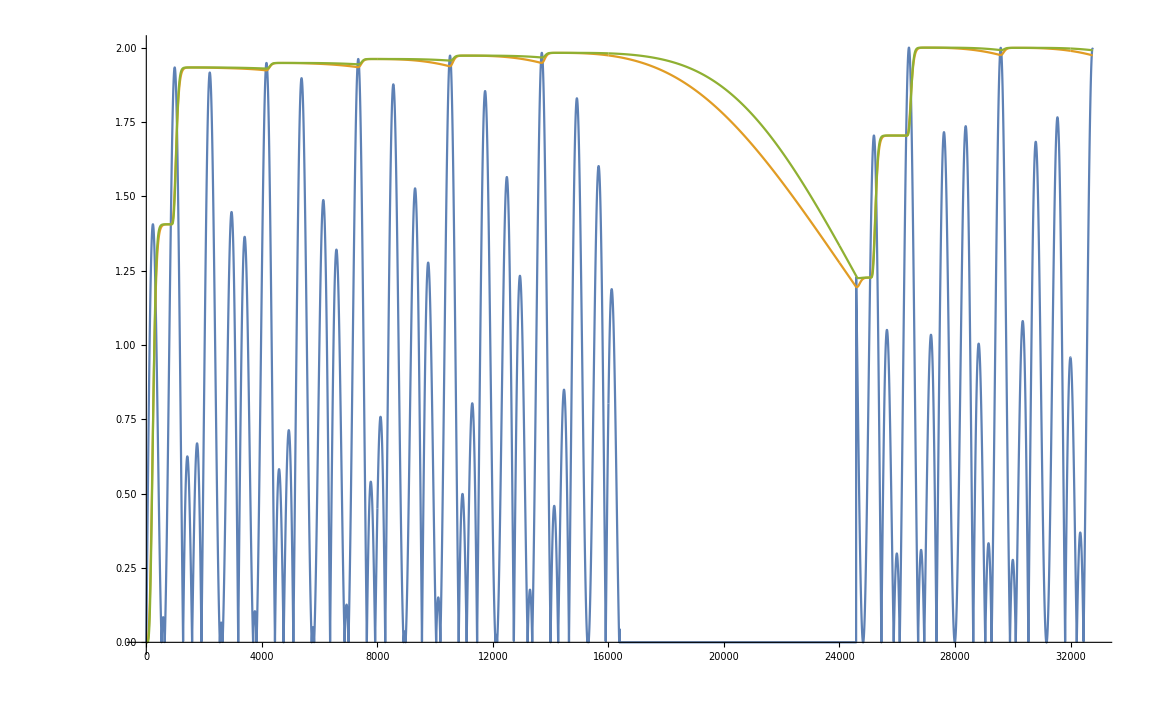

```mathematica
EnvelopeProcess[x_]:=Module[{i,ic1eq2Prev,F,ωca,ωcr,yz1, diff,output},
output = x;
ωca=1000;
ωcr = 5;
yz1 = 0;
ic1eq2Prev = ic1eq2;

For[i=1, i<=Length[x],i++,


diff =x[[i]] - yz1;
If[diff > 0,setSection1SmoothlyG[ωca];setSection2SmoothlyG[ωca]];
If[diff <=0  && ic1eq2*ic1eq2Prev<0,setSection1SmoothlyG[ωcr];setSection2SmoothlyG[ωcr];ic1eq2=0;ic1eq1=0];
ic1eq2Prev = ic1eq2;
output[[i]] = simperSVF1[output[[i]]]; 
output[[i]] = simperSVF2[output[[i]]];
yz1 = output[[i]];
];

output 
]

EnvelopeProcess1[x_]:=Module[{i,ic1eq1Prev,F,ωca,ωcr,yz1, diff,output},
output = x;
ωca=2000;
ωcr = 2.5;
yz1 = 0;
ic1eq1Prev = ic1eq1;

For[i=1, i<=Length[x],i++,


diff =x[[i]] - yz1;
If[diff > 0,setSection1SmoothlyG[ωca]];
If[diff <=0  && ic1eq1*ic1eq1Prev<0,setSection1SmoothlyG[ωcr];ic1eq1=0];
ic1eq1Prev = ic1eq1;
output[[i]] = simperSVF1[output[[i]]]; 
yz1 = output[[i]];
];

output 
]

EnvelopeProcess2[x_]:=Module[{i,ic1eq2Prev,F,ωca,ωcr,yz1, diff,output},
output = x;
ωca=100;
ωcr = 2.5;
yz1 = 0;
ic1eq2Prev = ic1eq2;

For[i=1, i<=Length[x],i++,


diff =x[[i]] - yz1;
If[diff > 0,setSection2SmoothlyG[ωca]];
If[diff <=0  && ic1eq2*ic1eq2Prev<0,setSection2SmoothlyG[ωcr];ic1eq2=0];
ic1eq2Prev = ic1eq2;
output[[i]] = simperSVF2[output[[i]]]; 
yz1 = output[[i]];
];

output 
]

EnvelopeProcessSeparateDual[X_]:=Module[{Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =200;
releaseFc = 2.5;
Q=0.5;

output =
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc,Q,sampleRate],
releaseFc,Q,sampleRate],
attackFc,Q,sampleRate],
attackFc,Q,sampleRate]; 


output
]

EnvelopeProcessSeparateSeries[X_]:=Module[{Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =500;
releaseFc = 2.5;
Q=0.5;

output =
attackOnlySVF[
releaseOnlySVF[
attackOnlySVF[
releaseOnlySVF[X,releaseFc,Q,sampleRate],
attackFc,Q,sampleRate],
releaseFc,Q,sampleRate],
attackFc,Q,sampleRate]; 


output
]

EnvelopeProcessSeparateTriple[X_]:=Module[{fMultiplier,Q,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =200;
releaseFc = 2.7;
Q=0.5;
fMultiplier = 1.5;

output =
attackOnlySVF[
attackOnlySVF[
attackOnlySVF[
releaseOnlySVF[
releaseOnlySVF[
releaseOnlySVF[X,releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
releaseFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate],
attackFc fMultiplier,Q,sampleRate]; 


output
]

EnvelopeProcessSeparateSingle[X_]:=Module[{Q,fMultiplier,attackFc,releaseFc,sampleRate,output},
sampleRate = 48000;
attackFc =500;
releaseFc = 2.5;
Q=0.5;
fMultiplier = 2.5;

output =attackOnlySVF[
releaseOnlySVF[X,releaseFc/fMultiplier,Q,sampleRate],
attackFc/fMultiplier,Q,sampleRate];


output
]

length = 2^15;
input = Table[Sin[15 2π N[x]]+Sin[60.445 2π N[x]],{x,0,length/sampleRate,1/sampleRate}];
input[[2Round[Length[input]/4];;3Round[Length[input]/4]]]=0;

 ListLinePlot[{Abs[input],EnvelopeProcessSeparateDual[Abs[input]],EnvelopeProcessSeparateTriple[Abs[input]]}] 
(* ListLinePlot[{Abs[input][[24570;;24590]],EnvelopeProcessSeparate[Abs[input]][[24570;;24590]]}]*)
```